```mathematica
Import["/Users/wagner.palacio/Documents/Projeto/Repos/SystemModeling/Projects/Monkeypox/SEIQREpidemiologyModel.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelModifications.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelingVisualizationFunctions.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/WL/SystemDynamicsInteractiveInterfacesFunctions.m"];
```

Importing from GitHub:  EpidemiologyModels.m

```mathematica
Clear[modelSEIQR];
modelSEIQR = 
  SEIQRModel[t, "InitialConditions" -> True, "RateRules" -> True, 
   "TotalPopulationRepresentation" -> "Constant"];
ModelGridTableForm[modelSEIQR]
```

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t],RateRules→# | Symbol | Value
1 | NP[0] | 100000
2 | β | 6.×10^-6
3 | α1 | 1/ζ
4 | α2 | 1/ζ
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 13
9 | λ | 31/4,InitialConditions→# | Equation
1 | SP[0]==99999
2 | EP[0]==0
3 | IP[0]==1
4 | QP[0]==0
5 | RP[0]==0|>

## Getting Data

```mathematica
cievsPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Pernambuco/Monkeypox%20-%20Pernambuco.csv", 
   "Dataset", "HeaderLines" -> 1];
cievsRECData :=Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Recife/Monkeypox%20-%20Recife.csv", "Dataset", 
   "HeaderLines" -> 1];
owdPEData := Import["https://raw.githubusercontent.com/globaldothealth/monkeypox/main/latest_deprecated.csv", "Dataset", "HeaderLines" -> 1];

dateFormat = {"Day", "/", "Month", "/", "Year"};
PEdataMap = cievsPEData // Normal;
RECdataMap = cievsRECData // Normal;
owdPEDataMap = Query[Select[StringContainsQ[ #Country, "Brazil"] && StringContainsQ[#Location, "Pernambuco"] && StringContainsQ[#Status, "confirmed"]&]] @ owdPEData;
```

#### Populações

```mathematica
(*pernambucoEntity = Entity["AdministrativeDivision", {"Pernambuco", "Brazil"}];
recifeEntity = Entity["City", {"Recife", "Pernambuco", "Brazil"}];
popProperty = "Population";*)

pernambucoPopulation = QuantityMagnitude[9674793]; (*IBGE 2022 - https://www.ibge.gov.br/cidades-e-estados/pe.html*)
recifePopulation =  QuantityMagnitude[1661017]; (*IBGE 2022 - https://www.ibge.gov.br/cidades-e-estados/pe.html*)
maleInfected = 82.6/100;(*Cievs/PE. Dados atualizados em 10.11.2022, 15h.*)
```

```mathematica
estimatedInitialSusceptiblePopulation = ((recifePopulation/pernambucoPopulation)*maleInfected)*recifePopulation
```

235552.

#### Confirmados

{Thu 21 Jul 2022→2,Fri 29 Jul 2022→4,Fri 5 Aug 2022→3,Sat 6 Aug 2022→3,Fri 12 Aug 2022→2,Tue 16 Aug 2022→1,Thu 18 Aug 2022→3,Wed 24 Aug 2022→4,Fri 26 Aug 2022→1,Mon 29 Aug 2022→1,Wed 31 Aug 2022→3,Thu 1 Sep 2022→14,Sun 4 Sep 2022→6,Tue 6 Sep 2022→1,Thu 8 Sep 2022→8,Fri 9 Sep 2022→4,Tue 13 Sep 2022→7,Wed 14 Sep 2022→23,Thu 15 Sep 2022→5,Fri 16 Sep 2022→12,Sat 17 Sep 2022→4,Tue 20 Sep 2022→7,Fri 23 Sep 2022→8,Tue 27 Sep 2022→2,Fri 30 Sep 2022→16,Tue 4 Oct 2022→10,Fri 7 Oct 2022→10,Tue 11 Oct 2022→0,Fri 14 Oct 2022→0,Tue 18 Oct 2022→1,Fri 21 Oct 2022→0,Tue 25 Oct 2022→3,Fri 28 Oct 2022→10,Tue 1 Nov 2022→8,Fri 4 Nov 2022→24,Tue 8 Nov 2022→3}

TimeSeries[…]

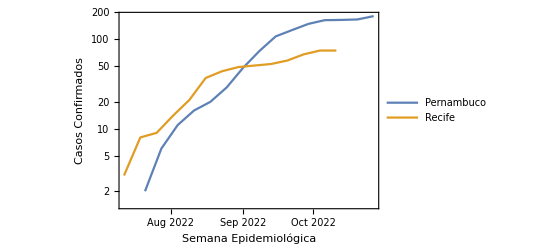

```mathematica
groupedByDateOWD = GroupBy[Normal[owdPEDataMap], FromDateString[#"Date_confirmation", {"Year", "-", "Month", "-", "Day"}]&,Length] // Normal;
groupedCievs= Map[FromDateString[#Inicio, dateFormat]-> #"Confirmados" &,PEdataMap];
confirmadosJoined = Union[groupedByDateOWD, Take[groupedCievs, {15,-1}]] 
totalJoinedSmoothed = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]], 7, "Align"->Left];

SmoothPeriod[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True], 7, "Align"->Left]
(*totalConfirmadosOWDPE=Smooth[Accumulate[TimeSeries[groupedByDateOWD, TemporalRegularity->True]]];*)
totalConfirmadosPE = 
    SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True]], 7, "Align"->Left];
totalConfirmadosREC = 
 SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #Confirmados} &,  RECdataMap],TemporalRegularity -> True]], 7, "Align"->Left];
DateListLogPlot[Tooltip[{totalJoinedSmoothed ,totalConfirmadosREC} ], 
 Joined -> True, PlotLegends -> {"Pernambuco", "Recife"}, 
 PlotMarkers -> False, GridLines -> Keys[confirmadosJoined],FrameLabel->{"Semana Epidemiológica","Casos Confirmados"}]
```

#### Prováveis

```mathematica
totalProvaveisPE =  SmoothPeriod[Accumulate[TimeSeries[ Map[{FromDateString[#Inicio, dateFormat], #"Prováveis"} &, PEdataMap], TemporalRegularity -> True]],7,"Align"->Left];
totalProvaveisREC = SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Prováveis"} &, RECdataMap], TemporalRegularity -> True]],7,"Align"->Left];
DateListLogPlot[Tooltip[{totalProvaveisPE, totalProvaveisREC} ], 
 Joined -> True, PlotLegends -> {"Pernambuco", "Recife"}, 
 PlotMarkers -> Automatic, GridLines -> Automatic];
```

#### Suspeitos

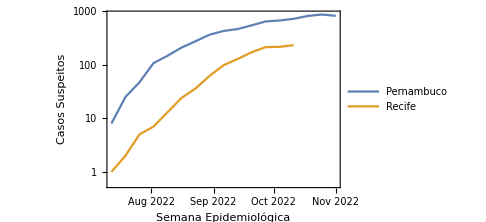

```mathematica
totalSuspeitosPE = 
  SmoothPeriod[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"} &, 
      PEdataMap],TemporalRegularity -> True]],7,"Align"->Left];
totalSuspeitosREC = 
SmoothPeriod[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"} &, RECdataMap], TemporalRegularity -> True]],7,"Align"->Left];
DateListLogPlot[Tooltip[{totalSuspeitosPE, totalSuspeitosREC} ], 
 Joined -> True, PlotLegends -> {"Pernambuco", "Recife"}, 
 PlotMarkers -> False, FrameLabel->{"Semana Epidemiológica","Casos Suspeitos"},ImageSize->Medium,GridLines -> False]
```

#### Notificados

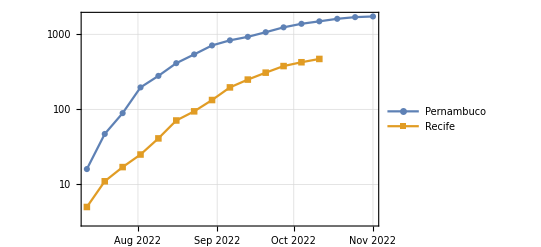

Keys::invrl: The argument joined is not a valid Association or a list of rules.

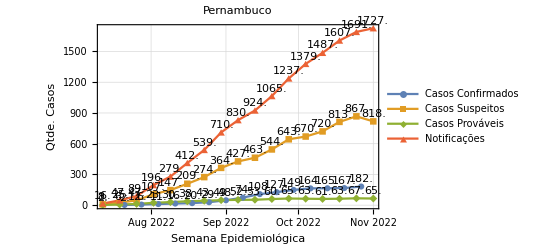

```mathematica
totalNotificadosPE = 
SmoothPeriod[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Notificados"} &, 
      PEdataMap],TemporalRegularity -> True]],7,"Align"->Left];
totalNotificadosREC = 
SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Notificados"} &, RECdataMap],TemporalRegularity -> True]],7,"Align"->Left];
DateListLogPlot[Tooltip[{totalNotificadosPE, totalNotificadosREC} ],  Joined -> True, PlotLegends -> {"Pernambuco", "Recife"},  PlotMarkers -> Automatic, GridLines -> Automatic]

DateListPlot[{totalJoinedSmoothed ,totalSuspeitosPE, totalProvaveisPE, totalNotificadosPE}->{#2&},LabelingFunction->(Placed[Last@#1,Above]&), 
 Joined -> True, PlotLegends -> {"Casos Confirmados", "Casos Suspeitos", "Casos Prováveis", "Notificações" }, 
 PlotMarkers -> Automatic, GridLines -> Keys[joined],FrameLabel->{"Semana Epidemiológica","Qtde. Casos"}, PlotLabel->"Pernambuco"]
```

## Dados Literatura

Alguns dados que tirei de  artigos sobre a dinâmica da Monkeypox que serão uteis para as formulas

#### Periodo de Incubação

```mathematica
incubation = Range[5, 21];
incubationPeriod = Mean[incubation];
incubationPeriod
```

13

#### Período de Infecção [1]

```mathematica
prodomalPhase = Range[0, 3];
rashPhase = Range[7, 21];
infectiousPeriod = Mean[Map[Median] @ {prodomalPhase, rashPhase}]
maxInfectiousPeriod = Max[prodomalPhase, rashPhase]
medianInfectiousPeriod = Flatten[ {prodomalPhase,rashPhase}]
```

31/4

21

{0,1,2,3,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

#### Taxa de Recuperação (γ)

De acordo com [2], γ ==1/λ, sendo λ a média do período de infecção total.

## Modelos

```mathematica
initialInfected =  Normal[totalJoinedSmoothed][[1]][[2]]
initialExposed = Normal[totalProvaveisPE][[1]][[2]]
initialQuarantine = Normal[totalSuspeitosPE][[1]][[2]]
realEPData =  <|"Exposed"-> Ceiling[totalSuspeitosPE["Values"]] // Normal|>
realIPData = <|"Infected"-> Ceiling[totalJoinedSmoothed["Values"]] // Normal|>
realQPData = <|"Quarantine"-> Ceiling[totalProvaveisPE["Values"]] // Normal|>
allData = Join[realEPData,realIPData,realQPData]
lsFocusParams = {β, ζ, λ};
```

2

2

8

<|Exposed→{8,25,47,107,147,209,274,364,427,463,544,643,670,720,813,867,818}|>

<|Infected→{2,6,11,16,20,29,48,74,108,127,149,164,165,167,182}|>

<|Quarantine→{2,6,12,23,30,38,43,49,52,53,60,65,63,61,63,67,65}|>

<|Exposed→{8,25,47,107,147,209,274,364,427,463,544,643,670,720,813,867,818},Infected→{2,6,11,16,20,29,48,74,108,127,149,164,165,167,182},Quarantine→{2,6,12,23,30,38,43,49,52,53,60,65,63,61,63,67,65}|>

```mathematica
modelSEIQR = SetRateRules[modelSEIQR, <|NP[0] -> estimatedInitialSusceptiblePopulation|>];
modelSEIQR = SetInitialConditions[modelSEIQR,
   <|SP[0] -> estimatedInitialSusceptiblePopulation -initialExposed- initialInfected-initialQuarantine,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>]; (* Subtrair do número da primeira semana epidemiológica*)
lsActualEquations = 
  Join[modelSEIQR["Equations"] //. 
    KeyDrop[modelSEIQR["RateRules"], lsFocusParams], 
   modelSEIQR["InitialConditions"]];
ResourceFunction["GridTableForm"][List /@ lsActualEquations]
```

# | 1
1 | SP'[t]==0.2 QP[t]-4.24535×10^-6 β IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/ζ+4.24535×10^-6 β IP[t] SP[t]
3 | IP'[t]==EP[t]/ζ-IP[t]/λ
4 | QP'[t]==EP[t]/ζ-(0.2+1/λ) QP[t]
5 | RP'[t]==IP[t]/λ+QP[t]/λ
6 | SP[0]==235540.
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

```mathematica
aSol = Association@
  Flatten@ParametricNDSolve[lsActualEquations, 
    Head /@ Keys[modelSEIQR["Stocks"]], {t, 0,52}, lsFocusParams];
```

```mathematica
opts = {PlotRange -> All, PlotLegends -> None, PlotTheme -> "Detailed", 
   PerformanceGoal -> "Speed", ImageSize -> 400};
lsPopulationKeys = GetPopulationSymbols[modelSEIQR, __ ~~ "Population"];
Manipulate[
 DynamicModule[{lsPopulationPlots}, 
  lsPopulationPlots = 
   ParametricSolutionsPlots[modelSEIQR["Stocks"], 
    KeyTake[aSol, lsPopulationKeys], {contactRate, incubationPeriod, 
     infectionPeriod}, nWeeks,
    "LogPlot" -> popLogPlotQ, "Together" -> popTogetherQ, 
    "Derivatives" -> popDerivativesQ, "DerivativePrefix" -> "Δ",
     opts];
 
  Multicolumn[lsPopulationPlots, nPlotColumns, Dividers -> All, 
   FrameStyle -> GrayLevel[0.8]]],
   
 {{contactRate, 6.3, StringJoin["Contact rate of the infected population (β) ", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 1, 10, 1, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Incubation period (ζ) in days"}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{infectionPeriod, 8, "Infection Period (λ) in days"}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week"}, 1, 52, 1, Appearance -> {"Open"}},
 {{popTogetherQ, True, "Plot populations together"}, {False, True}},
 {{popDerivativesQ, False, "Plot populations derivatives"}, {False, True}},
 {{popLogPlotQ, False, "LogPlot populations"}, {False, True}},
 {{nPlotColumns, 2, "Number of plot columns"}, Range[3]}, 
 ControlPlacement -> Left, ContinuousAction -> False]
```

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
Manipulate[
DynamicModule[{modelSEIQR=modelSEIQR,equations,aSol,lsPopulationPlots},
modelSEIQR = SetRateRules[modelSEIQR, <|NP[0] -> population|>];
modelSEIQR = SetInitialConditions[modelSEIQR,
   <|SP[0] ->  population -initialExposed- initialInfected-initialQuarantine,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>];
equations=Join[modelSEIQR["Equations"]//.KeyDrop[modelSEIQR["RateRules"],lsFocusParams],modelSEIQR["InitialConditions"]];
aSol=Association@Flatten@
ParametricNDSolve[equations,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams];

lsPopulationPlots=
ParametricSolutionsPlots[
modelSEIQR["Stocks"],
KeyTake[aSol,GetPopulationSymbols[modelSEIQR, __ ~~ "Population"]],
{contactRate, incubationPeriod,infectionPeriod},nWeeks,"Together"->False,opts];
    
Show[lsPopulationPlots⟦3⟧,ListPlot[PadRealData[realIPData,Round[incubationPeriod+padOffset],Round[infectionPeriod+padOffset]],PlotStyle->{Blue,Black,Red}]]
],
{{population,estimatedInitialSusceptiblePopulation/100,"População"},100,estimatedInitialSusceptiblePopulation,50,Appearance->{"Open"}},
{{padOffset,0,"deslocamento de dados reais"},-100,100,1,Appearance->{"Open"}},
 {{contactRate, 0.01, StringJoin["Taxa de Contágio (β)", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 0.01, 2, 0.01, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Período de Incubação (ζ) em dias"}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{infectionPeriod, 7, "Período de Infecção (λ) em dias"}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Semana Epidemiológica (t)"}, 1, 52, 1, Appearance -> {"Open"}},
 {{nPlotColumns, 2, "# de Colunas"}, Range[3]}, 
ControlPlacement->Left,ContinuousAction->False]
```

### Otimização de β

```mathematica
expostosJoined = Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"} &, PEdataMap];
```

```mathematica
totalInfectedOptimized = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],7,"Align"->Left]
```

TimeSeries[…]

```mathematica
firstDateInfected = First @ First@Normal[totalInfectedOptimized];
lastDateInfected = First @  Last@Normal[totalInfectedOptimized];
DateObject[First @ First@Normal[totalInfectedOptimized]]
```

Thu 21 Jul 2022 00:00:00GMT-3

```mathematica
ClearAll[modelSEIQR2];
modelSEIQR2 = SetRateRules[modelSEIQR, <|NP[0] -> estimatedInitialSusceptiblePopulation/100|>];
modelSEIQR2 = SetInitialConditions[modelSEIQR2,
   <|SP[0] ->  estimatedInitialSusceptiblePopulation/100-initialExposed- initialInfected-initialQuarantine ,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>];
lsActualEquations2 = Join[modelSEIQR2["Equations"]//.KeyDrop[modelSEIQR2["RateRules"],lsFocusParams],modelSEIQR2["InitialConditions"]];
ResourceFunction["GridTableForm"][List /@ lsActualEquations2]
asol2 = ParametricNDSolve[lsActualEquations2,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams];
```

# | 1
1 | SP'[t]==0.2 QP[t]-0.000424535 β IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/ζ+0.000424535 β IP[t] SP[t]
3 | IP'[t]==EP[t]/ζ-IP[t]/λ
4 | QP'[t]==EP[t]/ζ-(0.2+1/λ) QP[t]
5 | RP'[t]==IP[t]/λ+QP[t]/λ
6 | SP[0]==2343.52
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

#### Dados Totais, ajuste estatístico de β, ζ e λ

```mathematica
fitInfectedData={ToModelTime[firstDateInfected, #1], #2}& @@@ Normal[totalInfectedOptimized] //Echo[#, "", Multicolumn]&;
(*fitExposedData={toModelTime[firstDateExposed, #1], #2}& @@@ Normal[totalExpostosOptimized] //Echo[#, "", Multicolumn]&;*)
```

{0,2} | {28,20} | {56,108} | {84,165}
{7,6} | {35,29} | {63,127} | {91,167}
{14,11} | {42,48} | {70,149} | {98,182}
{21,16} | {49,74} | {77,164} |

```mathematica
infectedSol= IP[β,ζ,λ] /.asol2;
exposedSol = EP[β,ζ,λ] /.asol2;
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.432795 | 0.144859 | 2.98769 | 0.0113227
ζ | 5. | 6.2881 | 0.795153 | 0.441969
λ | 9.09259 | 1.48665 | 6.11614 | 0.0000520682

0.987511

0.984389

{β→0.432795,ζ→5.,λ→9.09259}

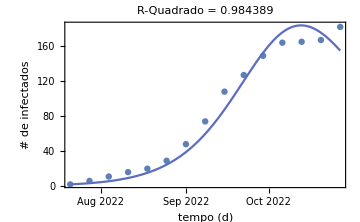

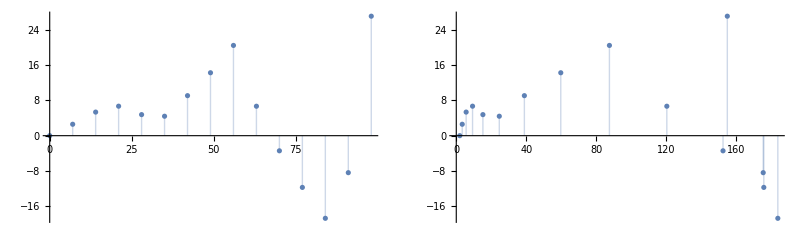

```mathematica
fitInfected=NonlinearModelFit[fitInfectedData,{infectedSol[t],5<=ζ<=21 && 0<=λ<=21 } ,{{β, 0.68}, {ζ,10},{λ,14}},t, Method->Automatic];
fitInfected["ParameterTable"]
fitInfected["RSquared"]
fitInfected["AdjustedRSquared"]
(*fitInfected["EstimatedVariance"]*)
fitInfected["BestFitParameters"]
(*fitInfected["Data"]*)
(*fitInfected["BestFit"]*)
FitWithDataPlot[fitInfected,{firstDateInfected,lastDateInfected} ]
ResidualsPlot[fitInfected]
(*ModelSensitivityPlot[ infectedSol,fitInfected,{{0,100},{-15,190}},{0.1,1,1}]*)
```

#### Ajuste estatístico, só β

```mathematica
lsActualEquations3 = Join[modelSEIQR2["Equations"]//.KeyDrop[modelSEIQR2["RateRules"],{β}],modelSEIQR2["InitialConditions"]];
ResourceFunction["GridTableForm"][List /@ lsActualEquations3]
asol3 = ParametricNDSolve[lsActualEquations3,{SP,EP,IP,QP, RP},{t,0,120},{β}];
```

# | 1
1 | SP'[t]==0.2 QP[t]-0.000424535 β IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/13+0.000424535 β IP[t] SP[t]
3 | IP'[t]==EP[t]/13-(4 IP[t])/31
4 | QP'[t]==EP[t]/13-0.329032 QP[t]
5 | RP'[t]==(4 IP[t])/31+(4 QP[t])/31
6 | SP[0]==2343.52
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

```mathematica
totalInfectedOptimized2 = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],21, "Align"-> Left] // Normal
(*totalSusceptibleOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal*)
firstDateInfected2 = First @ First@Normal[totalInfectedOptimized2]
lastDateInfected2 = First @  Last@ Normal[totalInfectedOptimized2]
fitInfectedData2={ToModelTime[firstDateInfected2, #1], #2}& @@@ Normal[totalInfectedOptimized2] //Echo[#, "", Multicolumn]&;
```

{{Thu 21 Jul 2022 00:00:00GMT-3,8},{Thu 11 Aug 2022 00:00:00GMT-3,23},{Thu 1 Sep 2022 00:00:00GMT-3,77},{Thu 22 Sep 2022 00:00:00GMT-3,147},{Thu 13 Oct 2022 00:00:00GMT-3,171}}

Thu 21 Jul 2022 00:00:00GMT-3

Thu 13 Oct 2022 00:00:00GMT-3

{0,8} | {42,77} | {84,171}
{21,23} | {63,147} |

{{Thu 21 Jul 2022 00:00:00GMT-3,8},{Thu 11 Aug 2022 00:00:00GMT-3,23},{Thu 1 Sep 2022 00:00:00GMT-3,77},{Thu 22 Sep 2022 00:00:00GMT-3,147},{Thu 13 Oct 2022 00:00:00GMT-3,171}}

NonlinearModelFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.680064 | 0.0220259 | 30.8756 | 6.5563×10^-6

0.974293

0.967866

{β→0.680064}

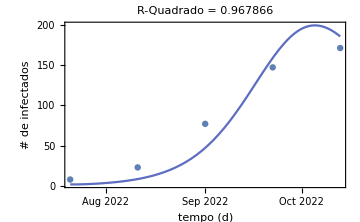

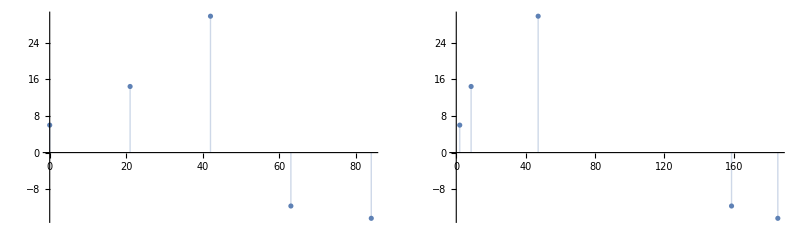

ModelSensitivityPlot[ParametricFunction[<>][β],FittedModel[InterpolatingFunction[…][t]],{{0,84},{-15,180}},{0.1}]

```mathematica
solution := ParametricNDSolve[lsActualEquations3,{SP,EP,IP,QP, RP},{t,First@First@fitInfectedData2,First@Last@fitInfectedData2},{β}];
{susceptible,infectedSol2}= {SP[β],IP[β]} /.solution;
current = Take[totalInfectedOptimized2,5]
fitInfected2=NonlinearModelFit[{ToModelTime[First@First@Normal[current], #1], #2}& @@@ Normal[current],infectedSol2[t],{{β,1}},t, Method->"QuasiNewton"];
fitInfected2["ParameterTable"]
fitInfected2["RSquared"]
fitInfected2["AdjustedRSquared"]
fitInfected2["BestFitParameters"]
FitWithDataPlot[fitInfected2,{First@First@Normal[current],First@Last@Normal[current]} ]
ResidualsPlot[fitInfected2]
ModelSensitivityPlot[ infectedSol2,fitInfected2,{{First@First@fitInfectedData2,First@Last@fitInfectedData2},{-15,180}},{0.1}]

(*susceptible=SP[N[First@Values[fitInfected2["BestFitParameters"]]]][84] /.solution*)
```

#### Com β Dinâmico

```mathematica
ClearAll[modelSEIQRDynamicBeta];
modelSEIQRDynamicBeta = SetRateRules[modelSEIQR, 
<|NP[0] -> Round[estimatedInitialSusceptiblePopulation/100],
IP[t /; t<=0]->IP[0],
β-> ((IP[t-2] +IP[t-1]+ IP[t])/(IP[t-2-ζ] + IP[t-1-ζ]+IP[t-ζ])),
ζ-> 21,
λ-> 7|>
];
modelSEIQRDynamicBeta = SetInitialConditions[modelSEIQRDynamicBeta,
   <|SP[0] ->  Round[estimatedInitialSusceptiblePopulation/100]-initialExposed- initialInfected-initialQuarantine ,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>];
lsActualEquationsDynamicBeta = Join[modelSEIQRDynamicBeta["Equations"]//.KeyDrop[modelSEIQRDynamicBeta["RateRules"], {}],modelSEIQRDynamicBeta["InitialConditions"]];
ModelGridTableForm[modelSEIQRDynamicBeta]
asolDynamicBeta = Association@Flatten@NDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP},{t,0,100}] 
 (*({#[20]})& /@ asolDynamicBeta *)
```

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t],RateRules→# | Symbol | Value
1 | NP[0] | 2356
2 | β | (IP[-2+t]+IP[-1+t]+IP[t])/(IP[-2+t-ζ]+IP[-1+t-ζ]+IP[t-ζ])
3 | α1 | 1/ζ
4 | α2 | 1/ζ
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 21
9 | λ | 7
10 | IP[t/;t≤0] | IP[0],InitialConditions→# | Equation
1 | SP[0]==2344
2 | EP[0]==2
3 | IP[0]==2
4 | QP[0]==8
5 | RP[0]==0|>

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

<|SP→InterpolatingFunction[…],EP→InterpolatingFunction[…],IP→InterpolatingFunction[…],QP→InterpolatingFunction[…],RP→InterpolatingFunction[…]|>

```mathematica
Manipulate[
DynamicModule[{lsPopulationPlots2},
lsPopulationPlots2=
ParametricSolutionsPlots[
modelSEIQRDynamicBeta["Stocks"],
KeyTake[asolDynamicBeta,GetPopulationSymbols[modelSEIQRDynamicBeta, __ ~~ "Population"]],{},nWeeks,"Together"->True,opts];
    
Show[lsPopulationPlots2[[1]],ListPlot[PadRealData[allData,Round[incubationPeriod+padOffset],Round[infectionPeriod+padOffset]],PlotStyle->{Blue,Black,Red}]]
],
{{population,estimatedInitialSusceptiblePopulation/100,"Population"},100,estimatedInitialSusceptiblePopulation,50,Appearance->{"Open"}},
{{padOffset,0,"real data padding offset"},-100,100,1,Appearance->{"Open"}},
 {{contactRate, 0.01, StringJoin["Contact rate of the infected population (β)", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 0.01, 2, 0.01, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 21, "Incubation period (ζ) in days "}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{infectionPeriod, 7, "Infection Period (λ) in days"}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week (t)"}, 1, 52, 1, Appearance -> {"Open"}},
 {{nPlotColumns, 2, "Number of plot columns"}, Range[3]}, 
ControlPlacement->Left,ContinuousAction->False]
```

```mathematica
totalInfectedOptimizedDynamic = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],21, "Align"-> Left] // Normal;
(*totalSusceptibleOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal*)
firstDateInfectedDynamic = First @ First@Normal[totalInfectedOptimizedDynamic];
lastDateInfectedDynamic = First @  Last@ Normal[totalInfectedOptimizedDynamic];
fitInfectedDataDynamic={ToModelTime[firstDateInfectedDynamic, #1], #2}& @@@ Normal[totalInfectedOptimizedDynamic] //Echo[#, "", Multicolumn]&;
(*asolDynamicBeta2 := NDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP},{t,0,98}] *)
```

{0,8} | {42,77} | {84,171}
{21,23} | {63,147} |

{{Thu 21 Jul 2022 00:00:00GMT-3,8},{Thu 11 Aug 2022 00:00:00GMT-3,23},{Thu 1 Sep 2022 00:00:00GMT-3,77},{Thu 22 Sep 2022 00:00:00GMT-3,147},{Thu 13 Oct 2022 00:00:00GMT-3,171}}

NonlinearModelFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

Power::infy: Infinite expression 1/0. encountered.

| Estimate | Standard Error | t-Statistic | P-Value
β | 1. | ComplexInfinity | 0. | 1.

FittedModel::bdfit: The sum of squared errors is not a non-negative number. The model may suffer from significant numerical error or may not be appropriate for the data.

-0.266715

FittedModel::bdfit: The sum of squared errors is not a non-negative number. The model may suffer from significant numerical error or may not be appropriate for the data.

-0.583394

{β→1.}

FittedModel::bdfit: The sum of squared errors is not a non-negative number. The model may suffer from significant numerical error or may not be appropriate for the data.

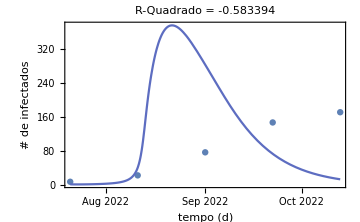

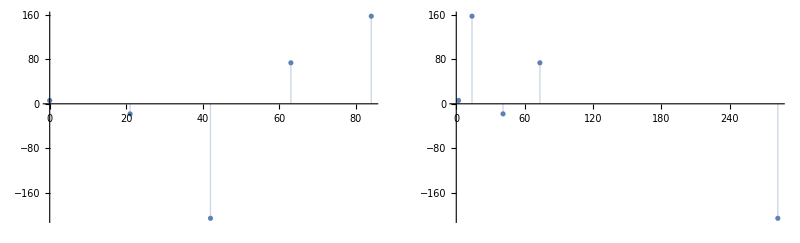

```mathematica
{infectedSolDynamic}= {IP} /.asolDynamicBeta;
currentDynamic = Take[totalInfectedOptimizedDynamic,5]
fitInfectedDynamic=NonlinearModelFit[{ToModelTime[First@First@Normal[currentDynamic], #1], #2}& @@@ Normal[currentDynamic],infectedSolDynamic[t],{β},t, Method->Automatic];
fitInfectedDynamic["ParameterTable"]
fitInfectedDynamic["RSquared"]
fitInfectedDynamic["AdjustedRSquared"]
fitInfectedDynamic["BestFitParameters"]
FitWithDataPlot[fitInfectedDynamic,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
ResidualsPlot[fitInfectedDynamic]


(*susceptible=SP[N[First@Values[fitInfected2["BestFitParameters"]]]][105] /.solution*)
```

## Modelo Final

```mathematica
finalFit = fitInfected2;
finalBeta = Values @@ finalFit["BestFitParameters"] *10
```

6.80064

```mathematica
modelSEIQRFinal = SetRateRules[modelSEIQR, <|NP[0] -> estimatedInitialSusceptiblePopulation,  β->finalBeta|>];
modelSEIQRFinal = SetInitialConditions[modelSEIQRFinal,
   <|SP[0] -> estimatedInitialSusceptiblePopulation -initialExposed- initialInfected-initialQuarantine,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>]; (* Subtrair do número da primeira semana epidemiológica*)
lsActualEquationsFinal = Join[modelSEIQRFinal["Equations"] //. KeyDrop[modelSEIQRFinal["RateRules"], {}], modelSEIQRFinal["InitialConditions"]];
ModelGridTableForm[modelSEIQRFinal]
ResourceFunction["GridTableForm"][List /@ lsActualEquationsFinal]
aSolFinal = NDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP},{t,0,60}]
```

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t],RateRules→# | Symbol | Value
1 | NP[0] | 235552.
2 | β | 6.80064
3 | α1 | 1/ζ
4 | α2 | 1/ζ
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 13
9 | λ | 31/4,InitialConditions→# | Equation
1 | SP[0]==235540.
2 | EP[0]==2
3 | IP[0]==2
4 | QP[0]==8
5 | RP[0]==0|>

# | 1
1 | SP'[t]==0.2 QP[t]-0.0000288711 IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/13+0.0000288711 IP[t] SP[t]
3 | IP'[t]==EP[t]/13-(4 IP[t])/31
4 | QP'[t]==EP[t]/13-0.329032 QP[t]
5 | RP'[t]==(4 IP[t])/31+(4 QP[t])/31
6 | SP[0]==235540.
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

{{SP→InterpolatingFunction[…],EP→InterpolatingFunction[…],IP→InterpolatingFunction[…],QP→InterpolatingFunction[…],RP→InterpolatingFunction[…]}}

```mathematica
aSolForPeaks = Association@Flatten@ParametricNDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP},{t,0,60}, {β}] ;
allValues =Map[ParametricFunctionValues[#,<|β-> finalBeta|>, 60]&, aSolForPeaks]
peaks = Map[FindPeaks[Last/@#]&,allValues]
(*lsFinal = ParametricSolutionsPlots[modelSEIQRFinal["Stocks"],KeyTake[aSolFinal,GetPopulationSymbols[modelSEIQRFinal, __ ~~ "Population"]],{β},100,"Together"->True,optsFinal]*)
(*ListLinePlot[{allValues[[1]], peaks[[1]]}&,
Joined->{True, False},
PlotStyle->{Automatic, PointSize[.03]}]*)
```

<|SP→{{0,235540.},{1,235527.},{2,235508.},{3,235475.},{4,235417.},{5,235314.},{6,235128.},{7,234797.},{8,234206.},{9,233153.},{10,231287.},{11,228001.},{12,222289.},{13,212579.},{14,196694.},{15,172322.},{16,138596.},{17,98613.8},{18,60229.},{19,31669.8},{20,15413.5},{21,8131.2},{22,5366.42},{23,4342.92},{24,3883.78},{25,3597.63},{26,3372.75},{27,3179.28},{28,3008.47},{29,2856.63},{30,2721.34},{31,2600.55},{32,2492.5},{33,2395.61},{34,2308.51},{35,2230.01},{36,2159.06},{37,2094.78},{38,2036.38},{39,1983.19},{40,1934.64},{41,1890.21},{42,1849.48},{43,1812.05},{44,1777.6},{45,1745.83},{46,1716.48},{47,1689.34},{48,1664.2},{49,1640.88},{50,1619.23},{51,1599.11},{52,1580.39},{53,1562.96},{54,1546.72},{55,1531.59},{56,1517.47},{57,1504.29},{58,1492.},{59,1480.51},{60,1469.79}},EP→{{0,2.},{1,15.0505},{2,31.762},{3,58.866},{4,106.177},{5,190.296},{6,340.471},{7,608.646},{8,1086.99},{9,1938.14},{10,3445.94},{11,6095.92},{12,10688.5},{13,18453.7},{14,31034.2},{15,49989.},{16,75338.},{17,103422.},{18,126689.},{19,138290.},{20,137580.},{21,129229.},{22,118200.},{23,107218.},{24,97201.2},{25,88272.6},{26,80321.7},{27,73207.2},{28,66806.8},{29,61022.9},{30,55777.9},{31,51009.2},{32,46665.},{33,42702.},{34,39083.1},{35,35775.7},{36,32751.6},{37,29985.3},{38,27454.1},{39,25137.7},{40,23017.6},{41,21076.8},{42,19300.2},{43,17673.7},{44,16184.6},{45,14821.3},{46,13573.2},{47,12430.4},{48,11384.2},{49,10426.2},{50,9549.17},{51,8746.13},{52,8010.87},{53,7337.65},{54,6721.23},{55,6156.81},{56,5639.98},{57,5166.73},{58,4733.37},{59,4336.53},{60,3973.12}},IP→{{0,2.},{1,2.37958},{2,3.75304},{3,6.50294},{4,11.5462},{5,20.6201},{6,36.871},{7,65.9328},{8,117.852},{9,210.475},{10,375.307},{11,667.368},{12,1180.91},{13,2071.85},{14,3582.21},{15,6045.61},{16,9823.19},{17,15109.6},{18,21656.1},{19,28685.2},{20,35229.5},{21,40614.7},{22,44622.9},{23,47342.1},{24,48972.9},{25,49723.8},{26,49776.4},{27,49280.5},{28,48358.1},{29,47108.7},{30,45613.5},{31,43938.7},{32,42138.3},{33,40256.7},{34,38329.8},{35,36386.6},{36,34450.6},{37,32540.3},{38,30670.5},{39,28852.4},{40,27094.5},{41,25403.1},{42,23782.6},{43,22235.6},{44,20763.7},{45,19367.2},{46,18045.6},{47,16797.9},{48,15622.4},{49,14517.},{50,13479.3},{51,12506.7},{52,11596.4},{53,10745.5},{54,9951.23},{55,9210.54},{56,8520.56},{57,7878.44},{58,7281.38},{59,6726.69},{60,6211.77}},QP→{{0,8.},{1,6.33575},{2,6.08662},{3,7.31991},{4,10.6148},{5,17.2415},{6,29.5986},{7,52.0423},{8,92.379},{9,164.491},{10,292.87},{11,520.184},{12,919.163},{13,1608.99},{14,2771.24},{15,4646.31},{16,7467.19},{17,11286.},{18,15754.5},{19,20115.4},{20,23572.7},{21,25719.1},{22,26602.3},{23,26507.8},{24,25751.2},{25,24588.2},{26,23200.5},{27,21710.4},{28,20197.},{29,18710.2},{30,17280.2},{31,15924.1},{32,14650.5},{33,13462.7},{34,12360.2},{35,11340.5},{36,10399.9},{37,9533.85},{38,8737.53},{39,8006.1},{40,7334.78},{41,6719.01},{42,6154.42},{43,5636.94},{44,5162.75},{45,4728.32},{46,4330.37},{47,3965.87},{48,3632.05},{49,3326.34},{50,3046.39},{51,2790.03},{52,2555.29},{53,2340.35},{54,2143.53},{55,1963.31},{56,1798.3},{57,1647.2},{58,1508.84},{59,1382.15},{60,1266.14}},RP→{{0,0.},{1,1.18069},{2,2.35133},{3,3.84149},{4,6.10375},{5,9.87362},{6,16.4235},{7,28.001},{8,48.6023},{9,85.338},{10,150.836},{11,267.401},{12,474.056},{13,837.879},{14,1470.67},{15,2549.06},{16,4327.54},{17,7120.18},{18,11223.},{19,16791.},{20,23755.8},{21,31858.2},{22,40759.9},{23,50141.2},{24,59742.7},{25,69369.7},{26,78880.5},{27,88174.5},{28,97181.4},{29,105853.},{30,114159.},{31,122079.},{32,129605.},{33,136735.},{34,143470.},{35,149819.},{36,155791.},{37,161398.},{38,166653.},{39,171572.},{40,176170.},{41,180463.},{42,184465.},{43,188194.},{44,191663.},{45,194889.},{46,197886.},{47,200668.},{48,203249.},{49,205641.},{50,207858.},{51,209910.},{52,211809.},{53,213565.},{54,215189.},{55,216690.},{56,218076.},{57,219355.},{58,220536.},{59,221626.},{60,222631.}}|>

<|SP→{{1,235540.}},EP→{{20,138290.}},IP→{{27,49776.4}},QP→{{1,8.},{23,26602.3}},RP→{{61,222631.}}|>

```mathematica
Clear[PadRealData];
PadRealData[aData:Association[(_String->_?VectorQ)..],incubationPeriod_?IntegerQ,infectiousPeriod_?IntegerQ]:=Block[{},Join[ConstantArray[0,incubationPeriod+infectiousPeriod],#]&/@aData];
```

```mathematica
(*Map[ParametricSolutionsPlots[#,<|β-> finalBeta|>, 100]&, aSolFinal]*)
(*PadRealData[peaks,13,7.75]*)
(*Show[lsFinal, peaks,PlotStyle->{Blue,Black,Red}]*)
(*Show[Plot[allValues,Joined->False,PlotRange->All]]*)
optsFinal={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
DynamicModule[{incubationPeriod=13,infectionPeriod=8,nWeeks=60,padOffset=-8},
DynamicModule[{modelSEIQR=modelSEIQRFinal,lsFinal},
lsFinal = ParametricSolutionsPlots[modelSEIQR["Stocks"],#,None,nWeeks,"Together"->True,optsFinal]&/@GroupBy[Normal@aSolFinal,#[[1,1]]&,Association];
(*Show[List@Plot[Map[Identity[#]&,Values[aSolFinal]],{t,0,100}, PlotRange->All,PlotLegends->None,PlotTheme->"Detailed"], ListPlot[peaks,PlotStyle-> {Red,Black,Blue}]]]]*)
Show[lsFinal[[1,1]], ListPlot[Labeled[#,#]&/@peaks, PlotLabels->Above,PlotLegends->None]]
]
]
```